This part is made so that people can understand that we ALWAYS have a resolution limitation when it comes to recording data.
The interspike interval between any two spikes will depend on the RATIO between the f1 and sRate but also on the phase.

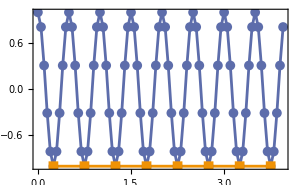

{0.5,0.5,0.5,0.5,0.5,0.5,0.5}

```mathematica
f=2;
ϕ=0;
sRate=20;
dat=Table[{t,1. Cos[2π f t+ϕ]},{t,0,4-1/sRate,1/sRate}];
peaks=dat[[FindPeaks[-dat[[;;,2]]][[;;,1]]]];
ListLinePlot[{dat,peaks},PlotMarkers->{Automatic, 10},ImageSize->300]
Differences[peaks[[;;,1]]]//N
```

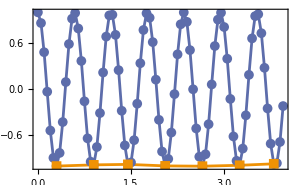

{0.6,0.55,0.6,0.6,0.6,0.55}

```mathematica
f=1.7;
ϕ=0;
sRate=20;
dat=Table[{t,1. Cos[2π f t+ϕ]},{t,0,4-1/sRate,1/sRate}];
peaks=dat[[FindPeaks[-dat[[;;,2]]][[;;,1]]]];
ListLinePlot[{dat,peaks},PlotMarkers->{Automatic, 10},ImageSize->300]
N[Differences[peaks[[;;,1]]]]
```

This is to show that if you partition a distribution, compute the means of each group separately and then take the histogram you will artificially lower the standard deviation
as it is statistically what happens when you average things out. 
In the following example I start with a single fake distribution with 10k elements, designed to have σ=1.

I will partition the dataset into 10 groups of 1000, and take the average of each before plotting a new distribution (shown in blue).

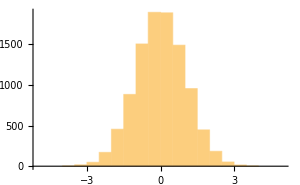
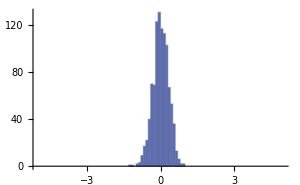

```mathematica
SeedRandom[20250202];
precisionData=RandomVariate[NormalDistribution[0,1],10000]; (* StandardDeviation of 1 *)
partitionedData=Mean/@Partition[precisionData,10];
MapThread[Histogram[#1,20,PlotRange->{{-5,5},Full},ChartStyle->#2,ImageSize->300]&,{{precisionData,partitionedData},{Automatic,blue}}]
```

```mathematica
StandardDeviation[precisionData]
StandardDeviation[Mean/@Partition[precisionData,10]]
```

1.01235

0.317931